0.62769

InterpolatingFunction::dmval: Input value {3.45093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.83355} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

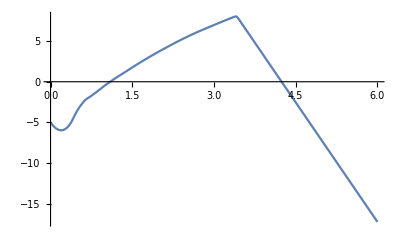

InterpolatingFunction::dmval: Input value {3.45083} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45063} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

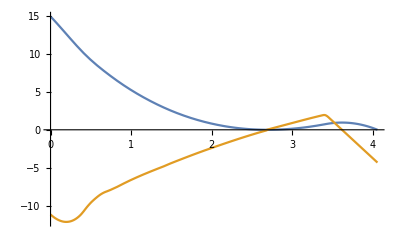

InterpolatingFunction::dmval: Input value {3.45069} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45026} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
ClearAll["Global`*"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);
g = 9.80655;
m = 1.0565;
v0 = -5;
s0 = 20;
burntime= 3.45;
tm = Solve[s0 + v0*tmax - g*tmax^2/2 ==0, tmax, NonNegativeReals];

vb[gamma_] := v0 - g*gamma;
sb[gamma_] := s0 + v0*gamma - g*gamma^2/2;

gamma = 0.62769

thrustCurve=Flatten[Import["C:\\Users\\rag\\Documents\\GitHub\\EPQ\\Rocket\\F15_Thrust.xlsx"] ,1];
ifun=Interpolation[thrustCurve, InterpolationOrder -> 1];
Thrust[t_] = Piecewise[{{ifun[t], 0< t < 3.45}}];
Plot[Thrust[t],{t,-2,5}, PlotRange->Full];

nsols = NDSolve[{s''[t]==Thrust[t]/m-g,s'[0] == vb[gamma], s[0] == sb[gamma], WhenEvent[s[t]== 0,If[t > 3.45, "StopIntegration", s'[t] -> 0]]},{s, s'},{t, 0, ∞}, "ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}, MaxStepSize -> 0.001];
Plot[{s[t]/. %, s'[t] /. %}, {t, 0,4.04}];
f= s'/. nsols[[1, 2]];
f[f["Domain"][[1,2]]];

ParametricNDSolve[{s''[x]==Thrust[x]/m-g,s'[0] == vo, s[0] == so, WhenEvent[s[x]== 0, If[x > 3.45, "StopIntegration", s'[x] -> 0]]}, s'[yu],{x, 0, ∞}, {vo , so}, "ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}];
y = s'[yu] /. %;
y[-5,20];
Plot[%, {yu, 0, 6}]

sol = ParametricNDSolve[{s''[x]==Thrust[x]/m-g,s'[0] == vo, s[0] == so, WhenEvent[s[x]== 0,If[x > 3.45, "StopIntegration", s'[x] -> 0]]},{s,s'},{x, 0, ∞}, {vo ∈ Reals, {so ,0, 100}}, "ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}, PrecisionGoal-> ∞, MaxStepSize -> 0.001];
h=s/. % ;
v = s' /. sol;
x =  0.62769;
vb[x];
sb[x];
ParametricPlot3D[{va, 20, h[va, 20]}, {va, -15, -5}];
Plot[{h[vb[x], sb[x]][t],v[vb[x], sb[x]][t]}, {t,0,4.04}];
Plot[{h[vb[x], sb[x]][t],h[vb[x], sb[x]]'[t]}, {t,0,h[vb[x], sb[x]]["Domain"][[1, 2]]}]
v[vb[x], sb[x]][v[vb[x], sb[x]]["Domain"][[1, 2]]];

(*velocities = Max[Abs[#' /@ (t/. Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}])]]& /@ Table[h[va, sa], {va, -15, 5, 1}, {sa, 0, 20, 1}]*)
Flatten[Table[h[va, sa], {va, -15, -5, 1}, {sa, 10, 20, 5}]]
FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}]& /@  {[h[-15, 0]]}
```